```mathematica
fBH=1+1.38*(OmegaH*rg/c)^2-9.2*(OmegaH*rg/c)^4
PhiBH=phibh/Sqrt[Mdot*rg^2*c]
phibh=Upsilon*5
P=(Kappa/(4*Pi*c))*PhiBH^2*OmegaF*(OmegaH-OmegaF)*fBH
```

1+(1.38 OmegaH^2 rg^2)/c^2-(9.2 OmegaH^4 rg^4)/c^4

phibh/(√(c Mdot rg^2))

5 Upsilon

1/(4 c^2 Mdot π rg^2)25 Kappa OmegaF (-OmegaF+OmegaH) (1+(1.38 OmegaH^2 rg^2)/c^2-(9.2 OmegaH^4 rg^4)/c^4) Upsilon^2

```mathematica
vff=Sqrt[2*G*M/r]
vr=ep*vff
Sigma=Mdot/(2*Pi*r*vr)
rho=Sigma/(2*hor*r)
(*
omegak=F*r^(-3/2)
vk=r*omegak
alpha=15/r
vr=alpha*vk*hor^2
Sigma=Mdot/(2*Pi*r*vr)
*)
Mdot=MdotH*(r/rg)^n
Br=Bz
G=rg*c^2/M
(*sols=Solve[G*M*Sigma/r^2==2*Br*Bz/(4*Pi),Bz]*)
sols=Solve[rho*vr^2*(2*hor*r)+G*M*Sigma/r^2==2*Br*Bz/(4*Pi),Bz]
myBz=sols[[2,1,2]]
rh=rg*(1+Sqrt[1-a^2])
router=rh
myUpsilon=Integrate[2*Pi*r*myBz,{r,0,router},Assumptions->{Re[n]>-3/2,(1+√(1-a^2)) rg>0,c>0}]
```

√2 √((c^2 rg)/r)

√2 ep √((c^2 rg)/r)

(MdotH (r/rg)^n)/(2 √2 ep π r √((c^2 rg)/r))

(MdotH (r/rg)^n)/(4 √2 ep hor π r^2 √((c^2 rg)/r))

MdotH (r/rg)^n

Bz

(c^2 rg)/M

{{Bz→-√((c^2 MdotH (r/rg)^n rg)/(√2 ep r^3 √((c^2 rg)/r))+(√2 c^2 ep MdotH (r/rg)^n rg)/(r^2 √((c^2 rg)/r)))},{Bz→√((c^2 MdotH (r/rg)^n rg)/(√2 ep r^3 √((c^2 rg)/r))+(√2 c^2 ep MdotH (r/rg)^n rg)/(r^2 √((c^2 rg)/r)))}}

√((c^2 MdotH (r/rg)^n rg)/(√2 ep r^3 √((c^2 rg)/r))+(√2 c^2 ep MdotH (r/rg)^n rg)/(r^2 √((c^2 rg)/r)))

(1+√(1-a^2)) rg

(1+√(1-a^2)) rg

$Aborted

12.9785 (1+√(1-a^2))^(5/4)

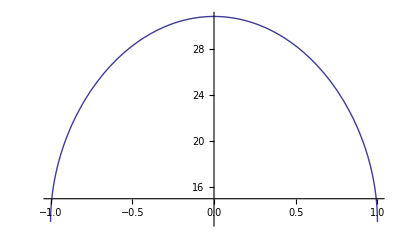

```mathematica
toplot1=myUpsilon//.{c->1,rg->1,n->0,MdotH->1,ep->0.1,hor->0.1,alpha->0.1,F->1}
Plot[toplot1,{a,-1,1}]
```

```mathematica
myP=P//.{Upsilon->myUpsilon}
```

1/(3 F hor^2 (5+2 n)^2)80 Kappa OmegaF (-OmegaF+OmegaH) π (r/rg)^-n rg^(-1-n) ((1+√(1-a^2)) rg)^(1/2 (5+2 n)) (1+(1.38 OmegaH^2 rg^2)/c^2-(9.2 OmegaH^4 rg^4)/c^4)

1.0472 a^2 √(1+√(1-a^2)) (1-(0.575 a^4)/((1+√(1-a^2))^4)+(0.345 a^2)/((1+√(1-a^2))^2))

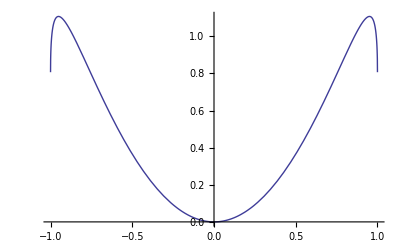

```mathematica
toplot2=myP//.{c->1,rg->1,n->0,MdotH->1,ep->0.1,Kappa->0.05,OmegaF->OmegaH/2,OmegaH->a/(2*rh),hor->0.1,alpha->0.1,F->1}
Plot[toplot2,{a,-1,1}]
```

0.00365423/hor^2

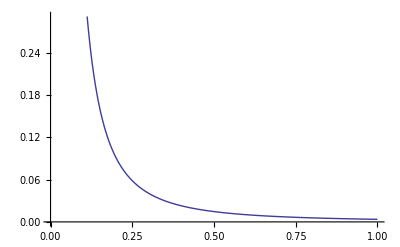

```mathematica
toplot3=myP//.{c->1,rg->1,n->0,MdotH->1,ep->0.1,Kappa->0.05,OmegaF->OmegaH/2,OmegaH->a/(2*rh),alpha->0.1,F->1,a->.5}
Plot[toplot3,{hor,0,1}]
```